```mathematica
px =.;
pz =.;
py =.;
p={px,py,pz};
r[x_,y_,z_]={x,y,z};
a={x,y,z};
ED[x_,y_,z_]=(3r[x,y,z](p.r[x,y,z])-p(x^2+y^2+z^2))/((x^2+y^2+z^2)^2.5);
EDNorm[x_,y_,z_]=√(((3 x (px x+py y+pz z)-px (x^2+y^2+z^2))/((x^2+y^2+z^2)^2.5))^2+((3 y (px x+py y+pz z)-py (x^2+y^2+z^2))/((x^2+y^2+z^2)^2.5))^2+((3 z (px x+py y+pz z)-pz (x^2+y^2+z^2))/((x^2+y^2+z^2)^2.5))^2);
EDHat[x_,y_,z_]=ED[x,y,z]/EDNorm[x,y,z];
Curv[x_,y_,z_]=Table[Sum[EDHat[x,y,z][[i]]*D[EDHat[x,y,z][[j]],a[[i]]],{i,1,3}],{j,1,3}];
```

```mathematica
ED[x,y,z]
```

{{(3 x^2)/((x^2+y^2+z^2)^2.5),(3 x y)/((x^2+y^2+z^2)^2.5),(3 x z)/((x^2+y^2+z^2)^2.5)},{(-x^2+3 x y-y^2-z^2)/((x^2+y^2+z^2)^2.5),(-x^2+2 y^2-z^2)/((x^2+y^2+z^2)^2.5),(-x^2-y^2+3 y z-z^2)/((x^2+y^2+z^2)^2.5)},{(3 x z)/((x^2+y^2+z^2)^2.5),(3 y z)/((x^2+y^2+z^2)^2.5),(3 z^2)/((x^2+y^2+z^2)^2.5)}}

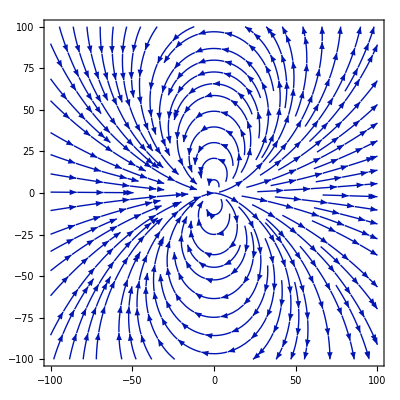

```mathematica
px = 100;
pz =0;
py = 0;
M = 100.0;
StreamPlot[{ED[x,y,0][[1]],ED[x,y,0][[2]]},{x,-M,M},{y,-M,M}]
```

```mathematica
px = 1;
pz = 0;
py = 0;
dataE=.
dataC=.
uMin=-M;
uMax = M;
vMin = -M;
vMax=M;
NumPoints=100000;
pts=RandomReal[{uMin,uMax},{NumPoints, 2}];
pts3D=Map[Append[#,0]&,pts];
p0=3;
dataE=Transpose[ED[pts3D[[All,1]],pts3D[[All,2]],pts3D[[All,3]]]];
dataE=(dataE[[All,1]]^2+dataE[[All,2]]^2+dataE[[All,3]]^2)^.5;
dataC=Transpose[Curv[pts3D[[All,1]],pts3D[[All,2]],pts3D[[All,3]]]];
dataC=(dataC[[All,1]]^2+dataC[[All,2]]^2+dataC[[All,3]]^2)^.5;
```

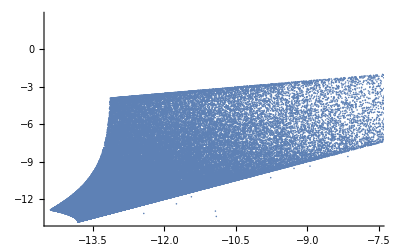

```mathematica
p1=ListPlot[Transpose[{Log[dataE],Log[dataC]}]];
p2=Plot[x/3,{x,-7,0}];
Show[p1,p2]
```

```mathematica
px =0;
pz =0;
py =1;
D[3x(r[x,y,z].p)-px*(x^2+y^2+z^2),x]
```

3 y

```mathematica
EDNorm[x,y,z]
```

(√(x^2+y^2+3 y^4+z^2))/((x^2+y^2+z^2)^2)

```mathematica
D[EDNorm[x,y,z],x]
```

x/((x^2+y^2+z^2)^2 √(x^2+y^2+3 y^4+z^2))-(4 x √(x^2+y^2+3 y^4+z^2))/((x^2+y^2+z^2)^3)

```mathematica
D[(x^2+y^2+z^2)^2.5,x]
```

5. x (x^2+y^2+z^2)^1.5

```mathematica
EDNorm[x_,y_,z_]=(√(3a^2+p^2(x^2+y^2+z^2)))/r^4
ED[x_,y_,z_]={(3x*a-px(x^2+y^2+z^2))/((x^2+y^2+z^2)^2.5),(3y*a-py(x^2+y^2+z^2))/((x^2+y^2+z^2)^2.5),(3z*a-pz(x^2+y^2+z^2))/((x^2+y^2+z^2)^2.5)};
ED[x,y,z]/EDNorm[x,y,z]
```

{(√3 √(x^2))/r^4,(√(x^2+4 y^2+z^2))/r^4,(√3 √(z^2))/r^4}

{{(3 x^2)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2)),(3 x y)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2)),(3 x z)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2))},{(-x^2+3 x y-y^2-z^2)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2)),(-x^2+2 y^2-z^2)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2)),(-x^2-y^2+3 y z-z^2)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2))},{(3 x z)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2)),(3 y z)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2)),(3 z^2)/((x^2+y^2+z^2)^0.5 √(x^2+y^2+3 y^4+z^2))}}

```mathematica
EHat[x_,y_,z_]={(3x*(px*x+py*y+pz*z)-px*(x^2+y^2+z^2))/(√((x^2+y^2+z^2)(3(px*x+py*y+pz*z)^2+(px^2+py^2+pz^2)(x^2+y^2+z^2)))),(3y*(px*x+py*y+pz*z)-py*(x^2+y^2+z^2))/(√((x^2+y^2+z^2)(3(px*x+py*y+pz*z)^2+(px^2+py^2+pz^2)(x^2+y^2+z^2)))),(3z*(px*x+py*y+pz*z)-pz*(x^2+y^2+z^2))/(√((x^2+y^2+z^2)(3(px*x+py*y+pz*z)^2+(px^2+py^2+pz^2)(x^2+y^2+z^2))))}
```

{(3 x y)/(√((x^2+y^2+z^2) (x^2+4 y^2+z^2))),(-x^2+2 y^2-z^2)/(√((x^2+y^2+z^2) (x^2+4 y^2+z^2))),(3 y z)/(√((x^2+y^2+z^2) (x^2+4 y^2+z^2)))}

```mathematica
D[EHat[x,y,z],x][[1]]
```

(3 y)/(√((x^2+y^2+z^2) (x^2+4 y^2+z^2)))-(3 x y (2 x (x^2+y^2+z^2)+2 x (x^2+4 y^2+z^2)))/(2 ((x^2+y^2+z^2) (x^2+4 y^2+z^2))^(3/2))

```mathematica
D[(x^2+y^2)^2,x]
```

4 x (x^2+y^2)

```mathematica
D[(x*px+y*py)^2,x]
```

0

```mathematica
EDNorm[x,y,z]=(√(3((px*x)^2+(py*y)^2+(pz*z)^2)^2+(px^2+py^2+pz^2)(x^2+y^2+z^2)))/((x^2+y^2+z^2)^2);
```

```mathematica
D[EDNorm[x,y,z],x][[1]]
```

x/((x^2+y^2+z^2)^2 √(x^2+y^2+3 y^4+z^2))

```mathematica
D[√(3((px*x)^2+(py*y)^2+(pz*z)^2)^2+(px^2+py^2+pz^2)(x^2+y^2+z^2)),x]
```

x/(√(x^2+y^2+3 y^4+z^2))